## Appell F_2

Loading the package

```mathematica
SetDirectory[NotebookDirectory[]];
<<ChisholmD.wl;
<<AppellF2.wl;
```

ChisholmD.wl 1.0
Authors : Souvik Bera & Tanay Pathak

AppellF2.wl v1.0\nAuthors : Souvik Bera & Tanay Pathak

```mathematica
?ChisholmD
```

## Appell F_2

CA around the point (0,0).

```mathematica
Block[{a=3/10,b1=4/10,b2=3/17,c1=1/5,c2=1/7,o=10},
ser=Sum[(Pochhammer[a,m+n]Pochhammer[b1,m]Pochhammer[b2,n])/(Pochhammer[c1,m]Pochhammer[c2,n]m!n!)(x)^m y^n,{m,0,2 o},{n,0,2 o}];

Caf200=ChisholmD[ser,{0,0,o},{x,y}]];
```

```mathematica
Block[{a=3/10,b1=4/10,b2=3/17,c1=1/5,c2=1/7},
valuesf200=Flatten[Join[{{"{x,y}","CA","Function","Error"}},Flatten[Table[If[Abs[x]+Abs[y]<1,
{N[{x,y}],N[Caf200,10],N[N[p1=AppellF2[a,b1,b2,c1,c2,x,y,50,150,F2show-> False],100],10],N[Abs[(p1-N[Caf200,100])/p1] 100,2]},Nothing],{x,-91/10,91/10,2/10},{y,-91/10,91/10,2/10}],1]],{1}]];
Labeled[Grid[valuesf200,Frame->All],"Table:1a",Top,LabelStyle->Directive[Bold,Red,19]]
```

{x,y} | CA | Function | Error
{-0.7,-0.1} | 0.7176113445 | 0.7176077258 | 0.0005
{-0.7,0.1} | 0.7246380769 | 0.7246292378 | 0.0012
{-0.5,-0.3} | 0.7582846936 | 0.752950892 | 0.71
{-0.5,-0.1} | 0.7715000769 | 0.7714998657 | 0.000027
{-0.5,0.1} | 0.7892128312 | 0.7892119264 | 0.00011
{-0.5,0.3} | 0.8040822017 | 0.803123702 | 0.12
{-0.3,-0.5} | 0.7786984122 | 0.7792425336 | 0.07
{-0.3,-0.3} | 0.8063786715 | 0.8063626308 | 0.002
{-0.3,-0.1} | 0.836524153 | 0.8365241513 | 2.1×10^-7
{-0.3,0.1} | 0.869849875 | 0.8698498613 | 1.6×10^-6
{-0.3,0.3} | 0.9057138533 | 0.9055751302 | 0.015
{-0.3,0.5} | 0.942860478 | 0.9394638015 | 0.36
{-0.1,-0.7} | 0.7969881987 | 0.7969884825 | 0.000036
{-0.1,-0.5} | 0.8307215036 | 0.8307215652 | 7.4×10^-6
{-0.1,-0.3} | 0.8701238321 | 0.870123833 | 1.×10^-7
{-0.1,-0.1} | 0.9170645508 | 0.9170645508 | 3.9×10^-13
{-0.1,0.1} | 0.9744040972 | 0.9744040972 | 4.1×10^-11
{-0.1,0.3} | 1.046742242 | 1.046742088 | 0.000015
{-0.1,0.5} | 1.141828658 | 1.141769629 | 0.0052
{-0.1,0.7} | 1.273394463 | 1.270849817 | 0.2
{0.1,-0.7} | 0.844405847 | 0.844410766 | 0.00058
{0.1,-0.5} | 0.8908884774 | 0.890889024 | 0.000061
{0.1,-0.3} | 0.9478851695 | 0.9478851788 | 9.8×10^-7
{0.1,-0.1} | 1.020357397 | 1.020357397 | 3.2×10^-11
{0.1,0.1} | 1.117408241 | 1.117408241 | 4.3×10^-12
{0.1,0.3} | 1.25823193 | 1.258231631 | 0.000024
{0.1,0.5} | 1.494179945 | 1.493552112 | 0.042
{0.1,0.7} | 2.33361026 | 2.034449677 | 15.
{0.3,-0.5} | 0.9611991532 | 0.9616785156 | 0.05
{0.3,-0.3} | 1.045101905 | 1.045183789 | 0.0078
{0.3,-0.1} | 1.159403989 | 1.159404087 | 8.4×10^-6
{0.3,0.1} | 1.32966649 | 1.329666586 | 7.2×10^-6
{0.3,0.3} | 1.70582769 | 1.62420975 | 5.
{0.3,0.5} | 0.132606888 | 2.330230632 | 94.
{0.5,-0.3} | 1.16902352 | 1.170339763 | 0.11
{0.5,-0.1} | 1.360497191 | 1.360527155 | 0.0022
{0.5,0.1} | 1.692823954 | 1.692673722 | 0.0089
{0.5,0.3} | 1.661346627 | 2.492432339 | 33.
{0.7,-0.1} | 1.686567234 | 1.687359945 | 0.047
{0.7,0.1} | 3.128438603 | 2.542388569 | 23.Table:1a

CA around the point (x,y).

```mathematica
Block[{a=3/10,b1=4/10,b2=3/17,c1=1/5,c2=1/7},valuesf200=Flatten[Join[{{"{x,y}","CA","Function","Error"}},Flatten[Table[If[Abs[x0]+Abs[y0]<1,
{Caf2ab=Chrisholm[ser,{x0,y0,5},{x,y}]/.{x->x0,y->y0};N[{x0,y0}],N[Caf2ab,10],N[N[p1=AppellF2[a,b1,b2,c1,c2,x0,y0,50,150,F2show-> False],100],10],N[Abs[(p1-N[Caf2ab,100])/p1] 100,2]},Nothing],{x0,-91/10,91/10,2/10},{y0,-91/10,91/10,2/10}],1]],{1}]];
Labeled[Grid[valuesf200,Frame->All],"Table:1b",Top,LabelStyle->Directive[Bold,Red,19]]
```

{x,y} | CA | Function | Error
{-0.7,-0.1} | 0.7176058955 | 0.7176077258 | 0.00026
{-0.7,0.1} | 0.7251883531 | 0.7246292378 | 0.077
{-0.5,-0.3} | 0.7529509945 | 0.752950892 | 0.000014
{-0.5,-0.1} | 0.7714998639 | 0.7714998657 | 2.4×10^-7
{-0.5,0.1} | 0.7892124711 | 0.7892119264 | 0.000069
{-0.5,0.3} | 0.8032356549 | 0.803123702 | 0.014
{-0.3,-0.5} | 0.7792426365 | 0.7792425336 | 0.000013
{-0.3,-0.3} | 0.8063626308 | 0.8063626308 | 3.3×10^-10
{-0.3,-0.1} | 0.8365241513 | 0.8365241513 | 5.7×10^-12
{-0.3,0.1} | 0.8698498613 | 0.8698498613 | 1.6×10^-9
{-0.3,0.3} | 0.9055751331 | 0.9055751302 | 3.2×10^-7
{-0.3,0.5} | 0.9394655842 | 0.9394638015 | 0.00019
{-0.1,-0.7} | 0.7969799731 | 0.7969884825 | 0.0011
{-0.1,-0.5} | 0.8307215569 | 0.8307215652 | 9.9×10^-7
{-0.1,-0.3} | 0.870123833 | 0.870123833 | 2.4×10^-11
{-0.1,-0.1} | 0.9170645508 | 0.9170645508 | 3.2×10^-21
{-0.1,0.1} | 0.9744040972 | 0.9744040972 | 1.7×10^-19
{-0.1,0.3} | 1.046742088 | 1.046742088 | 3.7×10^-11
{-0.1,0.5} | 1.141769653 | 1.141769629 | 2.1×10^-6
{-0.1,0.7} | 1.270896491 | 1.270849817 | 0.0037
{0.1,-0.7} | 0.8447793568 | 0.844410766 | 0.044
{0.1,-0.5} | 0.8908893832 | 0.890889024 | 0.00004
{0.1,-0.3} | 0.9478851788 | 0.9478851788 | 9.7×10^-10
{0.1,-0.1} | 1.020357397 | 1.020357397 | 1.×10^-19
{0.1,0.1} | 1.117408241 | 1.117408241 | 2.9×10^-19
{0.1,0.3} | 1.258231631 | 1.258231631 | 1.4×10^-9
{0.1,0.5} | 1.493550888 | 1.493552112 | 0.000082
{0.1,0.7} | 2.03167266 | 2.034449677 | 0.14
{0.3,-0.5} | 0.9617746234 | 0.9616785156 | 0.01
{0.3,-0.3} | 1.045183792 | 1.045183789 | 2.4×10^-7
{0.3,-0.1} | 1.159404087 | 1.159404087 | 9.1×10^-12
{0.3,0.1} | 1.329666586 | 1.329666586 | 2.1×10^-9
{0.3,0.3} | 1.624209737 | 1.62420975 | 8.2×10^-7
{0.3,0.5} | 2.329676824 | 2.330230632 | 0.024
{0.5,-0.3} | 1.170341465 | 1.170339763 | 0.00015
{0.5,-0.1} | 1.360527163 | 1.360527155 | 5.5×10^-7
{0.5,0.1} | 1.692671871 | 1.692673722 | 0.00011
{0.5,0.3} | 2.491789641 | 2.492432339 | 0.026
{0.7,-0.1} | 1.687377482 | 1.687359945 | 0.001
{0.7,0.1} | 2.538205755 | 2.542388569 | 0.16Table:1b

## Appell F_2: AC around (∞,∞)

Analytic continuation

```mathematica
F2expose[10][[1]]//Simplify
```

1/Abs[x]<1&&Abs[x/y]<1&&Abs[x/y]<Abs[x]/(1+Abs[x])&&1/Abs[y]<1&&Abs[x/y]+1/Abs[y]<1

```mathematica
F2expose[10][[2]]
```

(x^m (-y)^(-a-m) y^-n Gamma[-a+b2] Gamma[c2] Pochhammer[a,m+n] Pochhammer[b1,m] Pochhammer[1+a-c2,m+n])/(m! n! Gamma[b2] Gamma[-a+c2] Pochhammer[1+a-b2,m+n] Pochhammer[c1,m])+((-x)^-b1 x^-m (-y)^-b2 y^-n Gamma[a-b1-b2] Gamma[c1] Gamma[c2] Pochhammer[b1,m] Pochhammer[b2,n] Pochhammer[1+b1-c1,m] Pochhammer[1+b2-c2,n])/(m! n! Gamma[a] Gamma[-b1+c1] Gamma[-b2+c2] Pochhammer[1-a+b1+b2,m+n])+((-x)^(-a+b2) x^(-m+n) (-y)^-b2 y^-n Gamma[a-b2] Gamma[-a+b1+b2] Gamma[c1] Gamma[c2] Pochhammer[a-b2,m-n] Pochhammer[b2,n] Pochhammer[1+a-b2-c1,m-n] Pochhammer[1+b2-c2,n])/(m! n! Gamma[a] Gamma[b1] Gamma[-a+b2+c1] Gamma[-b2+c2] Pochhammer[1+a-b1-b2,m-n])

Region of convergence

```mathematica
F2expose[10][[1]]//Simplify
```

1/Abs[x]<1&&Abs[x/y]<1&&Abs[x/y]<Abs[x]/(1+Abs[x])&&1/Abs[y]<1&&Abs[x/y]+1/Abs[y]<1

```mathematica
Block[{a=Rationalize[1.23],b1=Rationalize[1.54],b2=Rationalize[1.67],c1=Rationalize[2.11],c2=Rationalize[2.39],o0=10},

series1=Sum[(Pochhammer[b1,m] Pochhammer[b2,n] Pochhammer[1+b1-c1,m] Pochhammer[1+b2-c2,n])/(m! n! Pochhammer[1-a+b1+b2,m+n])X^m Y^n,{m,0,2 o0},{n,0,2 o0}];CAseries100=((-x)^-b1 (-y)^-b2  Gamma[a-b1-b2] Gamma[c1] Gamma[c2])/(Gamma[a] Gamma[-b1+c1] Gamma[-b2+c2])ChisholmD[series1,{0,0,o0},{X,Y}]/.{X->1/x,Y-> 1/y};

series2=Sum[(Pochhammer[a-b2,m-n] Pochhammer[b2,n] Pochhammer[1+a-b2-c1,m-n] Pochhammer[1+b2-c2,n])/(m! n! Pochhammer[1+a-b1-b2,m-n])(X)^m(Y)^n,{m,0,2 o0},{n,0,2 o0}];CAseries200=((-x)^(-a+b2) (-y)^-b2 Gamma[a-b2] Gamma[-a+b1+b2] Gamma[c1] Gamma[c2])/(Gamma[a] Gamma[b1] Gamma[-a+b2+c1] Gamma[-b2+c2])ChisholmD[series2,{0,0,o0},{X,Y}]/.{X-> 1/x,Y->x/y};


series3=Sum[(Pochhammer[a,m+n] Pochhammer[b1,m] Pochhammer[1+a-c2,m+n])/(m! n!  Pochhammer[1+a-b2,m+n] Pochhammer[c1,m])(X)^m Y^n,{m,0,2 o0},{n,0,2 o0}];CAseries300=((-y)^-a Gamma[-a+b2] Gamma[c2])/(Gamma[b2] Gamma[-a+c2])ChisholmD[series3,{0,0,o0},{X,Y}]/.{X->-x/y,Y->1/y};


CAac00= CAseries100+CAseries200+CAseries300;
]
```

Numerical test

1) Values in first quadrant.

```mathematica
Block[{a=Rationalize[1.23],b1=Rationalize[1.54],b2=Rationalize[1.67],c1=Rationalize[2.11],c2=Rationalize[2.39]},
valuesf2ac001=Flatten[Join[{{"{x,y}","CA","Function","Error"}},
Flatten[Table[If[1/Abs[x]<1&&Abs[x/y]<1&&Abs[x/y]<Abs[x]/(1+Abs[x])&&1/Abs[y]<1&&Abs[x/y]+1/Abs[y]<1,
{N[{x,y}],N[CAac00,10],N[N[p1=AppellF2[a,b1,b2,c1,c2,x,y,50,150,F2show-> False],150],10],N[Abs[(p1-N[CAac00,100])/p1] 100,2]},Nothing],{x,5,15},{y,5,15}],1]],{1}]];
Labeled[Grid[valuesf2ac001,Frame->All],"Table:2a",Top,LabelStyle->Directive[Bold,Red,19]]
```

{x,y} | CA | Function | Error
{5.,7.} | -0.08002100935+0.0651865101 ⅈ | -0.08002093973+0.0651864487 ⅈ | 0.00009
{5.,8.} | -0.0715969633+0.0588444758 ⅈ | -0.07159694383+0.0588444586 ⅈ | 0.000028
{5.,9.} | -0.06478066345+0.0536069946 ⅈ | -0.06478065727+0.0536069891 ⅈ | 9.8×10^-6
{5.,10.} | -0.05914307265+0.049207729 ⅈ | -0.05914307047+0.0492077271 ⅈ | 3.8×10^-6
{5.,11.} | -0.05439795912+0.045459839 ⅈ | -0.05439795829+0.0454598383 ⅈ | 1.6×10^-6
{5.,12.} | -0.05034624236+0.0422283679 ⅈ | -0.05034624202+0.0422283675 ⅈ | 7.×10^-7
{5.,13.} | -0.04684475379+0.0394133674 ⅈ | -0.04684475364+0.0394133673 ⅈ | 3.3×10^-7
{5.,14.} | -0.04378766925+0.0369392082 ⅈ | -0.04378766918+0.0369392082 ⅈ | 1.6×10^-7
{5.,15.} | -0.04109494944+0.0347475853 ⅈ | -0.04109494941+0.0347475853 ⅈ | 8.5×10^-8
{6.,8.} | -0.06334876098+0.0526468503 ⅈ | -0.06334875074+0.0526468413 ⅈ | 0.000017
{6.,9.} | -0.05765922769+0.0482088935 ⅈ | -0.05765922444+0.0482088906 ⅈ | 5.8×10^-6
{6.,10.} | -0.05291485045+0.0444537122 ⅈ | -0.0529148493+0.0444537112 ⅈ | 2.2×10^-6
{6.,11.} | -0.04889236065+0.0412335267 ⅈ | -0.04889236021+0.0412335263 ⅈ | 9.2×10^-7
{6.,12.} | -0.04543520651+0.0384406899 ⅈ | -0.04543520632+0.0384406898 ⅈ | 4.1×10^-7
{6.,13.} | -0.04242993777+0.0359948567 ⅈ | -0.04242993769+0.0359948566 ⅈ | 1.9×10^-7
{6.,14.} | -0.03979208996+0.0338347918 ⅈ | -0.03979208992+0.0338347917 ⅈ | 9.6×10^-8
{6.,15.} | -0.03745734539+0.031912972 ⅈ | -0.03745734537+0.0319129719 ⅈ | 5.×10^-8
{7.,9.} | -0.05206025377+0.0438395357 ⅈ | -0.05206025173+0.0438395339 ⅈ | 4.×10^-6
{7.,10.} | -0.04798596715+0.0405827898 ⅈ | -0.04798596644+0.0405827892 ⅈ | 1.5×10^-6
{7.,11.} | -0.0445103433+0.0377743059 ⅈ | -0.04451034302+0.0377743057 ⅈ | 6.3×10^-7
{7.,12.} | -0.04150663463+0.0353261547 ⅈ | -0.04150663451+0.0353261546 ⅈ | 2.8×10^-7
{7.,13.} | -0.03888243022+0.0331722913 ⅈ | -0.03888243017+0.0331722913 ⅈ | 1.3×10^-7
{7.,14.} | -0.03656852924+0.0312620803 ⅈ | -0.03656852922+0.0312620802 ⅈ | 6.5×10^-8
{7.,15.} | -0.03451194552+0.029556006 ⅈ | -0.03451194551+0.029556006 ⅈ | 3.3×10^-8
{8.,10.} | -0.04395897338+0.0373587877 ⅈ | -0.04395897287+0.0373587872 ⅈ | 1.2×10^-6
{8.,11.} | -0.04091188734+0.0348796816 ⅈ | -0.04091188715+0.0348796814 ⅈ | 4.8×10^-7
{8.,12.} | -0.03826594994+0.0327090716 ⅈ | -0.03826594985+0.0327090716 ⅈ | 2.1×10^-7
{8.,13.} | -0.0359442608+0.0307916657 ⅈ | -0.03594426077+0.0307916657 ⅈ | 9.9×10^-8
{8.,14.} | -0.03388896184+0.0290848638 ⅈ | -0.03388896182+0.0290848638 ⅈ | 4.9×10^-8
{8.,15.} | -0.03205555025+0.027555266 ⅈ | -0.03205555024+0.027555266 ⅈ | 2.5×10^-8
{9.,11.} | -0.03788883676+0.0324150599 ⅈ | -0.03788883661+0.0324150598 ⅈ | 4.1×10^-7
{9.,12.} | -0.03553238645+0.0304723261 ⅈ | -0.03553238638+0.0304723261 ⅈ | 1.8×10^-7
{9.,13.} | -0.03345682486+0.0287500782 ⅈ | -0.03345682483+0.0287500782 ⅈ | 8.3×10^-8
{9.,14.} | -0.03161297838+0.0272119544 ⅈ | -0.03161297837+0.0272119544 ⅈ | 4.×10^-8
{9.,15.} | -0.0299628813+0.025829334 ⅈ | -0.0299628813+0.025829334 ⅈ | 2.1×10^-8
{10.,12.} | -0.03318694911+0.0285343314 ⅈ | -0.03318694906+0.0285343314 ⅈ | 1.6×10^-7
{10.,13.} | -0.03131549068+0.0269756658 ⅈ | -0.03131549066+0.0269756658 ⅈ | 7.4×10^-8
{10.,14.} | -0.02964778608+0.0255795378 ⅈ | -0.02964778607+0.0255795378 ⅈ | 3.6×10^-8
{10.,15.} | -0.02815102391+0.0243211336 ⅈ | -0.02815102391+0.0243211336 ⅈ | 1.8×10^-8
{11.,13.} | -0.02944755635+0.0254164032 ⅈ | -0.02944755633+0.0254164032 ⅈ | 7.×10^-8
{11.,14.} | -0.02792878444+0.0241413166 ⅈ | -0.02792878443+0.0241413166 ⅈ | 3.4×10^-8
{11.,15.} | -0.02656216045+0.0229891806 ⅈ | -0.02656216044+0.0229891806 ⅈ | 1.7×10^-8
{12.,14.} | -0.02640917202+0.022862698 ⅈ | -0.02640917201+0.0228626979 ⅈ | 3.3×10^-8
{12.,15.} | -0.02515433098+0.0218024201 ⅈ | -0.02515433098+0.0218024201 ⅈ | 1.7×10^-8
{13.,15.} | -0.02389610946+0.0207370312 ⅈ | -0.02389610945+0.0207370312 ⅈ | 1.7×10^-8Table:2a

```mathematica
Block[{a=Rationalize[1.23],b1=Rationalize[1.54],b2=Rationalize[1.67],c1=Rationalize[2.11],c2=Rationalize[2.39]},
valuesf2ac001=Flatten[Join[{{"{x,y}","CA","Function","Error"}},
Flatten[Table[If[1/Abs[x]<1&&Abs[x/y]<1&&Abs[x/y]<Abs[x]/(1+Abs[x])&&1/Abs[y]<1&&Abs[x/y]+1/Abs[y]<1,
{N[{x,y}],N[CAac00,10],N[N[p1=AppellF2[a,b1,b2,c1,c2,x,y,50,150,F2show-> False],150],10],N[Abs[(p1-N[CAac00,100])/p1] 100,2]},Nothing],{x,5,15},{y,5,15}],1]],{1}]];
Labeled[Grid[valuesf2ac001,Frame->All],"Table:2a",Top,LabelStyle->Directive[Bold,Red,19]]
```

2) Values in second quadrant.

```mathematica
Block[{a=Rationalize[1.23],b1=Rationalize[1.54],b2=Rationalize[1.67],c1=Rationalize[2.11],c2=Rationalize[2.39]},
valuesf2ac002=Flatten[Join[{{"{x,y}","CA","Function","Error"}},
Flatten[Table[If[1/Abs[x]<1&&Abs[x/y]<1&&Abs[x/y]<Abs[x]/(1+Abs[x])&&1/Abs[y]<1&&Abs[x/y]+1/Abs[y]<1,
{N[{x,y}],N[CAac00,10],N[N[p1=AppellF2[a,b1,b2,c1,c2,x,y,50,150,F2show-> False],150],10],N[Abs[(p1-N[CAac00,100])/p1] 100,2]},Nothing],{x,-15,-5},{y,5,15}],1]],{1}]];
Labeled[Grid[valuesf2ac002,Frame->All],"Table:2b",Top,LabelStyle->Directive[Bold,Red,19]]
```

{x,y} | CA | Function | Error
{-13.,15.} | -0.131113507-0.161371993 ⅈ | -0.131156274-0.1614470649 ⅈ | 0.042
{-12.,14.} | -0.142571768-0.1718855247 ⅈ | -0.142617829-0.1719647885 ⅈ | 0.041
{-12.,15.} | -0.1288025566-0.121349786 ⅈ | -0.1288043996-0.121352896 ⅈ | 0.002
{-11.,13.} | -0.155993178-0.1838409781 ⅈ | -0.156043337-0.1839260057 ⅈ | 0.041
{-11.,14.} | -0.1399563404-0.128014265 ⅈ | -0.1399582741-0.128017521 ⅈ | 0.002
{-11.,15.} | -0.1268800686-0.0968033275 ⅈ | -0.1268802396-0.0968036159 ⅈ | 0.00021
{-10.,12.} | -0.17190631-0.1975564861 ⅈ | -0.171961696-0.1976494756 ⅈ | 0.041
{-10.,13.} | -0.1530014886-0.135406903 ⅈ | -0.1530035619-0.135410394 ⅈ | 0.002
{-10.,14.} | -0.1377550065-0.101048382 ⅈ | -0.1377551878-0.101048688 ⅈ | 0.00021
{-10.,15.} | -0.1250867486-0.0786163423 ⅈ | -0.125086774-0.0786163853 ⅈ | 0.000034
{-9.,11.} | -0.191043124-0.2134507315 ⅈ | -0.191105449-0.2135549964 ⅈ | 0.042
{-9.,12.} | -0.1684411146-0.143638013 ⅈ | -0.1684434111-0.143641888 ⅈ | 0.002
{-9.,13.} | -0.1504504515-0.105557566 ⅈ | -0.1504506526-0.105557906 ⅈ | 0.00021
{-9.,14.} | -0.1356810035-0.0810073128 ⅈ | -0.135681032-0.081007361 ⅈ | 0.000035
{-9.,15.} | -0.1233213864-0.0638590061 ⅈ | -0.123321392-0.0638590155 ⅈ | 7.9×10^-6
{-8.,10.} | -0.21444534-0.2320855797 ⅈ | -0.214517457-0.2322065552 ⅈ | 0.045
{-8.,11.} | -0.1869691803-0.152831807 ⅈ | -0.1869718525-0.15283633 ⅈ | 0.0022
{-8.,12.} | -0.1654426556-0.110300492 ⅈ | -0.1654428934-0.110300894 ⅈ | 0.00024
{-8.,13.} | -0.1480198447-0.0832909425 ⅈ | -0.1480198791-0.0832910007 ⅈ | 0.00004
{-8.,14.} | -0.1336201067-0.0646817787 ⅈ | -0.1336201135-0.0646817902 ⅈ | 9.×10^-6
{-8.,15.} | -0.1215290516-0.0512009126 ⅈ | -0.1215290533-0.0512009154 ⅈ | 2.5×10^-6
{-7.,9.} | -0.243644356-0.2542318183 ⅈ | -0.24373155-0.2543792632 ⅈ | 0.049
{-7.,10.} | -0.2095686356-0.163119664 ⅈ | -0.2095719783-0.163125333 ⅈ | 0.0025
{-7.,11.} | -0.1833845197-0.115198969 ⅈ | -0.183384826-0.115199488 ⅈ | 0.00028
{-7.,12.} | -0.1625488861-0.0853178798 ⅈ | -0.1625489312-0.0853179562 ⅈ | 0.000048
{-7.,13.} | -0.1455783621-0.0650653437 ⅈ | -0.1455783712-0.065065359 ⅈ | 0.000011
{-7.,14.} | -0.1315073826-0.0506096693 ⅈ | -0.1315073849-0.0506096731 ⅈ | 3.2×10^-6
{-7.,15.} | -0.1196696947-0.039911454 ⅈ | -0.1196696954-0.0399114551 ⅈ | 1.×10^-6
{-6.,8.} | -0.2809809601-0.280973193 ⅈ | -0.281094078-0.2811663746 ⅈ | 0.056
{-6.,9.} | -0.2376760025-0.174619016 ⅈ | -0.2376806207-0.174626851 ⅈ | 0.0031
{-6.,10.} | -0.2051935999-0.120082832 ⅈ | -0.2051940373-0.120083572 ⅈ | 0.00036
{-6.,11.} | -0.1798730229-0.0868350792 ⅈ | -0.1798730883-0.0868351898 ⅈ | 0.000064
{-6.,12.} | -0.1596049935-0.0647462514 ⅈ | -0.1596050066-0.0647462736 ⅈ | 0.000015
{-6.,13.} | -0.1430465569-0.0492588863 ⅈ | -0.1430465601-0.0492588918 ⅈ | 4.2×10^-6
{-6.,14.} | -0.1292919877-0.0379809403 ⅈ | -0.1292919887-0.0379809419 ⅈ | 1.4×10^-6
{-6.,15.} | -0.1177061302-0.0295310459 ⅈ | -0.1177061305-0.0295310465 ⅈ | 5.×10^-7
{-5.,7.} | -0.3302084957-0.313874775 ⅈ | -0.33037208-0.314155814 ⅈ | 0.071
{-5.,8.} | -0.2734706473-0.187375542 ⅈ | -0.273477871-0.187387784 ⅈ | 0.0043
{-5.,9.} | -0.2321969287-0.124600604 ⅈ | -0.2321976284-0.124601787 ⅈ | 0.00052
{-5.,10.} | -0.2008309728-0.0874045929 ⅈ | -0.200831077-0.0874047692 ⅈ | 0.000094
{-5.,11.} | -0.1762454634-0.0632985459 ⅈ | -0.176245484-0.0632985808 ⅈ | 0.000022
{-5.,12.} | -0.1565090764-0.046764393 ⅈ | -0.1565090814-0.0467644015 ⅈ | 6.1×10^-6
{-5.,13.} | -0.1403563958-0.0349604223 ⅈ | -0.1403563972-0.0349604247 ⅈ | 1.9×10^-6
{-5.,14.} | -0.1269225831-0.02627561 ⅈ | -0.1269225835-0.0262756108 ⅈ | 7.×10^-7
{-5.,15.} | -0.1155967635-0.0197330568 ⅈ | -0.1155967636-0.0197330571 ⅈ | 2.8×10^-7Table:2b

3) Values in the third quadrant.

```mathematica
Block[{a=Rationalize[1.23],b1=Rationalize[1.54],b2=Rationalize[1.67],c1=Rationalize[2.11],c2=Rationalize[2.39]},
valuesf2ac003=Flatten[Join[{{"{x,y}","CA","Function","Error"}},
Flatten[Table[If[1/Abs[x]<1&&Abs[x/y]<1&&Abs[x/y]<Abs[x]/(1+Abs[x])&&1/Abs[y]<1&&Abs[x/y]+1/Abs[y]<1,
{N[{x,y}],N[CAac00,10],N[N[p1=AppellF2[a,b1,b2,c1,c2,x,y,50,150,F2show-> False],150],10],N[Abs[(p1-N[CAac00,100])/p1] 100,2]},Nothing],{x,-15,-5},{y,-15,-5}],1]],{1}]];
Labeled[Grid[valuesf2ac003,Frame->All],"Table:2c",Top,LabelStyle->Directive[Bold,Red,19]]
```

{x,y} | CA | Function | Error
{-13.,-15.} | 0.02655751606 | 0.02655751606 | 2.5×10^-8
{-12.,-15.} | 0.02774836293 | 0.02774836292 | 2.6×10^-8
{-12.,-14.} | 0.02893068774 | 0.02893068774 | 4.9×10^-9
{-11.,-15.} | 0.02905558917 | 0.02905558916 | 2.9×10^-8
{-11.,-14.} | 0.03032857956 | 0.03032857956 | 6.2×10^-9
{-11.,-13.} | 0.03171949919 | 0.0317194992 | 1.3×10^-8
{-10.,-15.} | 0.03049841658 | 0.03049841658 | 4.5×10^-9
{-10.,-14.} | 0.03187442909 | 0.03187442909 | 8.8×10^-9
{-10.,-13.} | 0.03338108786 | 0.03338108786 | 1.1×10^-8
{-10.,-12.} | 0.03503865604 | 0.03503865605 | 3.7×10^-8
{-9.,-15.} | 0.03210090142 | 0.03210090142 | 3.8×10^-9
{-9.,-14.} | 0.03359487551 | 0.03359487551 | 7.7×10^-9
{-9.,-13.} | 0.03523448269 | 0.0352344827 | 1.6×10^-8
{-9.,-12.} | 0.03704281254 | 0.03704281255 | 3.3×10^-8
{-9.,-11.} | 0.03904830527 | 0.03904830531 | 8.2×10^-8
{-8.,-15.} | 0.03389368839 | 0.03389368839 | 2.7×10^-9
{-8.,-14.} | 0.0355239237 | 0.0355239237 | 5.7×10^-9
{-8.,-13.} | 0.03731764148 | 0.03731764148 | 1.3×10^-8
{-8.,-12.} | 0.03930139568 | 0.03930139569 | 2.9×10^-8
{-8.,-11.} | 0.04150801733 | 0.04150801736 | 7.×10^-8
{-8.,-10.} | 0.04397865659 | 0.04397865667 | 1.8×10^-7
{-7.,-15.} | 0.03591665338 | 0.03591665338 | 1.×10^-9
{-7.,-14.} | 0.0377059141 | 0.0377059141 | 2.6×10^-9
{-7.,-13.} | 0.03968017747 | 0.03968017748 | 6.7×10^-9
{-7.,-12.} | 0.04187030604 | 0.04187030605 | 1.7×10^-8
{-7.,-11.} | 0.04431462543 | 0.04431462545 | 4.7×10^-8
{-7.,-10.} | 0.04706139747 | 0.04706139753 | 1.3×10^-7
{-7.,-9.} | 0.05017238101 | 0.05017238121 | 3.9×10^-7
{-6.,-15.} | 0.03822305271 | 0.03822305271 | 1.5×10^-9
{-6.,-14.} | 0.04020018867 | 0.04020018867 | 2.2×10^-9
{-6.,-13.} | 0.04238864963 | 0.04238864963 | 2.9×10^-9
{-6.,-12.} | 0.04482474834 | 0.04482474834 | 2.4×10^-9
{-6.,-11.} | 0.04755380988 | 0.04755380988 | 3.7×10^-9
{-6.,-10.} | 0.05063322479 | 0.05063322481 | 3.3×10^-8
{-6.,-9.} | 0.05413686947 | 0.05413686955 | 1.6×10^-7
{-6.,-8.} | 0.05816168842 | 0.05816168882 | 6.8×10^-7
{-5.,-15.} | 0.0408863787 | 0.0408863787 | 5.4×10^-9
{-5.,-14.} | 0.04308880476 | 0.04308880475 | 9.8×10^-9
{-5.,-13.} | 0.04553531522 | 0.04553531521 | 1.8×10^-8
{-5.,-12.} | 0.0482692583 | 0.04826925828 | 3.5×10^-8
{-5.,-11.} | 0.05134506667 | 0.05134506664 | 7.×10^-8
{-5.,-10.} | 0.0548321135 | 0.05483211342 | 1.4×10^-7
{-5.,-9.} | 0.05882033484 | 0.05882033467 | 2.9×10^-7
{-5.,-8.} | 0.06342866471 | 0.06342866434 | 5.8×10^-7
{-5.,-7.} | 0.06881812267 | 0.06881812208 | 8.6×10^-7Table:2c

4) Values in the fourth quadrant.

```mathematica
Block[{a=Rationalize[1.23],b1=Rationalize[1.54],b2=Rationalize[1.67],c1=Rationalize[2.11],c2=Rationalize[2.39]},
valuesf2ac004=Flatten[Join[{{"{x,y}","CA","Function","Error"}},
Flatten[Table[If[1/Abs[x]<1&&Abs[x/y]<1&&Abs[x/y]<Abs[x]/(1+Abs[x])&&1/Abs[y]<1&&Abs[x/y]+1/Abs[y]<1,
{N[{x,y}],N[CAac00,10],N[N[p1=AppellF2[a,b1,b2,c1,c2,x,y,50,150,F2show-> False],150],10],N[Abs[(p1-N[CAac00,100])/p1] 100,2]},Nothing],{x,5,15},{y,-15,-5}],1]],{1}]];
Labeled[Grid[valuesf2ac004,Frame->All],"Table:2d",Top,LabelStyle->Directive[Bold,Red,19]]
```

{x,y} | CA | Function | Error
{5.,-15.} | 0.08472607959-0.0647031512 ⅈ | 0.08472607937-0.0647031524 ⅈ | 1.1×10^-6
{5.,-14.} | 0.09099197888-0.0730631584 ⅈ | 0.09099197831-0.0730631615 ⅈ | 2.6×10^-6
{5.,-13.} | 0.09809776628-0.0833077424 ⅈ | 0.09809776462-0.083307751 ⅈ | 6.9×10^-6
{5.,-12.} | 0.1061889434-0.0960806939 ⅈ | 0.1061889381-0.0960807217 ⅈ | 0.00002
{5.,-11.} | 0.1154246915-0.112338445 ⅈ | 0.1154246719-0.112338548 ⅈ | 0.000065
{5.,-10.} | 0.125952702-0.1335596509 ⅈ | 0.125952617-0.1335601009 ⅈ | 0.00025
{5.,-9.} | 0.137831179-0.1621469607 ⅈ | 0.137830704-0.1621494496 ⅈ | 0.0012
{5.,-8.} | 0.150794938-0.2022603359 ⅈ | 0.150791307-0.2022793718 ⅈ | 0.0077
{5.,-7.} | 0.1635286-0.261648181 ⅈ | 0.163483364-0.2618853166 ⅈ | 0.078
{6.,-15.} | 0.08067170524-0.0741631592 ⅈ | 0.08067170498-0.0741631605 ⅈ | 1.2×10^-6
{6.,-14.} | 0.08619195092-0.083942915 ⅈ | 0.0861919502-0.0839429187 ⅈ | 3.2×10^-6
{6.,-13.} | 0.0923205855-0.09599028838 ⅈ | 0.0923205833-0.09599030012 ⅈ | 9.×10^-6
{6.,-12.} | 0.0990943782-0.1111114078 ⅈ | 0.0990943702-0.1111114495 ⅈ | 0.000028
{6.,-11.} | 0.106489998-0.1305271435 ⅈ | 0.106489965-0.1305273176 ⅈ | 0.00011
{6.,-10.} | 0.114327589-0.1561759433 ⅈ | 0.114327417-0.1561768456 ⅈ | 0.00047
{6.,-9.} | 0.122022884-0.1913319788 ⅈ | 0.122021685-0.1913382649 ⅈ | 0.0028
{6.,-8.} | 0.127885585-0.2420011933 ⅈ | 0.127872668-0.2420689211 ⅈ | 0.025
{7.,-15.} | 0.0763269512-0.08325714073 ⅈ | 0.0763269508-0.0832571427 ⅈ | 1.8×10^-6
{7.,-14.} | 0.0809905937-0.09450623656 ⅈ | 0.0809905926-0.09450624254 ⅈ | 4.9×10^-6
{7.,-13.} | 0.0859728878-0.1084591416 ⅈ | 0.0859728839-0.1084591621 ⅈ | 0.000015
{7.,-12.} | 0.0911589698-0.1261309084 ⅈ | 0.0911589541-0.1261309906 ⅈ | 0.000054
{7.,-11.} | 0.0962557078-0.1491047933 ⅈ | 0.0962556311-0.1491051952 ⅈ | 0.00023
{7.,-10.} | 0.100558662-0.1800055756 ⅈ | 0.100558171-0.1800081474 ⅈ | 0.0013
{7.,-9.} | 0.102327723-0.2235742716 ⅈ | 0.102323087-0.2235986052 ⅈ | 0.01
{8.,-15.} | 0.071614598-0.09229529453 ⅈ | 0.0716145973-0.09229529799 ⅈ | 3.×10^-6
{8.,-14.} | 0.0752695263-0.1051389463 ⅈ | 0.0752695242-0.1051389578 ⅈ | 9.×10^-6
{8.,-13.} | 0.0788641957-0.1212184669 ⅈ | 0.0788641873-0.121218511 ⅈ | 0.000031
{8.,-12.} | 0.0820564857-0.1418455891 ⅈ | 0.082056447-0.1418457923 ⅈ | 0.00013
{8.,-11.} | 0.0841141354-0.1691651958 ⅈ | 0.0841139068-0.1691663953 ⅈ | 0.00065
{8.,-10.} | 0.0833701601-0.2070068801 ⅈ | 0.083368245-0.2070169578 ⅈ | 0.0046
{9.,-15.} | 0.0664194094-0.10154634 ⅈ | 0.0664194081-0.101546347 ⅈ | 5.8×10^-6
{9.,-14.} | 0.0688474782-0.1162049659 ⅈ | 0.0688474734-0.1162049914 ⅈ | 0.000019
{9.,-13.} | 0.0706903069-0.1347993085 ⅈ | 0.0706902857-0.1347994199 ⅈ | 0.000074
{9.,-12.} | 0.0712307112-0.1591136583 ⅈ | 0.0712305955-0.1591142668 ⅈ | 0.00036
{9.,-11.} | 0.0689174976-0.1923084145 ⅈ | 0.0689166299-0.1923130015 ⅈ | 0.0023
{10.,-15.} | 0.0605735022-0.1112968632 ⅈ | 0.0605734992-0.1112968788 ⅈ | 0.000013
{10.,-14.} | 0.0614451166-0.1281354988 ⅈ | 0.0614451044-0.1281355631 ⅈ | 0.000046
{10.,-13.} | 0.0609450749-0.1499189087 ⅈ | 0.060945013-0.1499192357 ⅈ | 0.00021
{10.,-12.} | 0.0576472734-0.1793048145 ⅈ | 0.0576468536-0.1793070481 ⅈ | 0.0012
{11.,-15.} | 0.0538204107-0.1219142261 ⅈ | 0.0538204034-0.1219142647 ⅈ | 0.000029
{11.,-14.} | 0.0526004195-0.1415531172 ⅈ | 0.0526003849-0.1415533005 ⅈ | 0.00012
{11.,-13.} | 0.0486907771-0.1677827059 ⅈ | 0.0486905632-0.1677838509 ⅈ | 0.00067
{12.,-15.} | 0.0457362348-0.1339519621 ⅈ | 0.0457362148-0.1339520683 ⅈ | 0.000076
{12.,-14.} | 0.0414577878-0.1575378766 ⅈ | 0.0414576734-0.1575384885 ⅈ | 0.00038
{13.,-15.} | 0.0355355954-0.1483899398 ⅈ | 0.0355355307-0.1483902788 ⅈ | 0.00023Table:2d

## Total regions

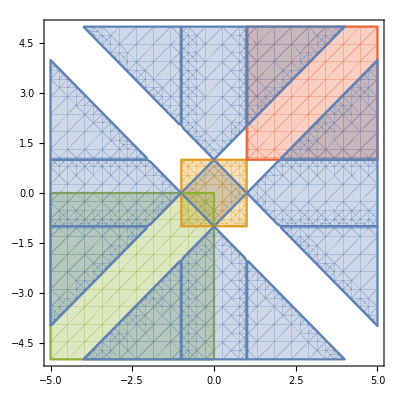

```mathematica
Show[RegionPlot[{Abs[x]+Abs[y]<1,Abs[x]<1&& Abs[y]<1,x<0&&y<0,x>1&&y>1},{x,-5,5},{y,-5,5}],r1,r2,r3,r4]
```